Санкт-Петербургский государственный экономический университет

# Курсовая работа

# Реализация алгоритма поиска сильно стабильного распределения врачей по клиникам

Выполнила:
Лепёхина А.В.
ПМ-1802

Санкт-Петербург
2019

## Формулировка задачи

```mathematica
2
```

## Исходные данные

Список предпочтений резидентов | Список предпочтений госпиталей
 | 
r_1 | {h_2,h_3,h_1}
r_2 | {h_2,h_1}
r_3 | {h_3,h_2,h_1}
r_4 | {h_2,h_3}
r_5 | {h_2,h_1,h_3}
r_6 | {h_3} | h_1 | {r_2,r_1,r_3,r_5} | 3
h_2 | {r_3,r_2,r_1,r_4,r_5} | 2
h_3 | {r_4,r_5,r_1,r_3,r_6} | 1

```mathematica
3
```

## Связи в списках предпочтений

Стороны могут добавлять связи в свои списки предпочтений:

h_1: { r_2,{r_1,r_5},r_4 }  3

Множество ℜ из n резидентов  образует связь длины n в списке предпочтений h, если h не предпочитает резидента r_i резиденту  r_j  ∀ r_i ,r_j ∈ ℜ

Множество ℋ из m госпиталей  образует связь длины m в списке предпочтений r, если r не предпочитает госпиталь h_i госпиталю  h_j  ∀ h_i ,h_j ∈  ℋ

Определение стабильного размещения не распространяется на версию задачи со связями

```mathematica
4
```

## Расширение понятия блокирующей пары

Пара (r,h) - блокирующая, если выполняется хотя бы одно из условий:

a) Для обеих сторон пары существуют более подходящие варианты

⇒ слабая стабильность

b) Ни одной из сторон пары не станет хуже

⇒ супер стабильность

c) Для одной из сторон пары будет лучше, а для другой стороны ситуация не станет хуже

⇒ сильная стабильность

```mathematica
5
```

## Алгоритм поиска сильно-стабильного распределения

repeat {
  	while some resident r  is free and has a non-empty list
    		for each hospital h at the head of r’s list {
    			provisionally assign r to h ;
    				if h is fully-subscribed or over-subscribed {
    					for each resident r' dominated on h’s list
    					delete the pair (r', h) } }
    	form the reduced provisional assignment graph ;
    	find the critical set Z of residents ;
    	for each hospital h  N(Z)
    		for each resident r  in the tail of h’s list
    			delete the pair (r , h) ;
   } until Z == ∅;
   let G be the final provisional assignment graph ;
   let M be a feasible matching in G ;
   if M is strongly stable 
   	output M ;
   else
   	no strongly stable matchings exists;

```mathematica
6
```

## Исходные данные

Список предпочтений резидентов | Список предпочтений госпиталей
 | 
r_1 | {{h_2,h_3},{h_1}}
r_2 | {{h_2},{h_1}}
r_3 | {{h_3},{h_2},{h_1}}
r_4 | {{h_2},{h_3}}
r_5 | {{h_2},{h_1,h_3}}
r_6 | {{h_3}} | h_1 | {{r_2},{r_1,r_3},{r_5}} | 3
h_2 | {{r_3},{r_2},{r_1,r_4,r_5}} | 2
h_3 | {{r_4,r_5},{r_1,r_3},{r_6}} | 1

списки предпочтений со связями

```mathematica
7
```

## Формирование временных распределений и удаление доминируемых резидентов

repeat {
  	while some resident r  is free and has a non-empty list
    		for each hospital h at the head of r’s list {
    			provisionally assign r  to h ;
    				if h is fully-subscribed or over-subscribed {
    					for each resident r' dominated on h’s list
    						delete the pair (r', h) } }
    	form the reduced provisional assignment graph ;
    	find the critical set Z of residents ;
    	for each hospital h  N(Z)
    		for each resident r  in the tail of h’s list
    			delete the pair (r , h) ;
   } until Z == ∅;
   let G be the final provisional assignment graph ;
   let M be a feasible matching in G ;
   if M is strongly stable 
   	output M ;
   else
   	no strongly stable matchings exists;

```mathematica
8
```

## Временное распределение и доминируемый резидент

Список предпочтений резидентов | Список предпочтений госпиталей
 | 
r_1 | {{h_2,h_3},{h_1}}
r_2 | {{h_2},{h_1}}
r_3 | {{h_3},{h_2},{h_1}}
r_4 | {{h_2},{h_3}}
r_5 | {{h_2},{h_1,h_3}}
r_6 | {{h_3}} | h_1 | {{r_2},{r_1,r_3},{r_5}} | 3
h_2 | {{r_3},{r_2},{r_1,r_4,r_5}} | 2
h_3 | {{r_4,r_5},{r_1,r_3},r_6} | 1

{h_2, h_3} - голова списка предпочтений резидента r_1

r_6- доминируемый резидент в списке предпочтений госпиталя h_3

```mathematica
9
```

## Все временные распределения, полученные на первой итерации алгоритма

Список предпочтений резидентов | Список предпочтений госпиталей
 | 
r_1 | {{h_2,h_3},{h_1}}
r_2 | {h_2,{h_1}}
r_3 | {{h_3},{h_2},{h_1}}
r_4 | {{h_2},{h_3}}
r_5 | {{h_2},{h_1,h_3}}
r_6 | {{h_3}} | h_1 | {{r_2},{r_1,r_3},{r_5}} | 3
h_2 | {{r_3},{r_2},{r_1,r_4,r_5}} | 2
h_3 | {{r_4,r_5},{r_1,r_3},r_6} | 1

```mathematica
10
```

## Граф временных распределений

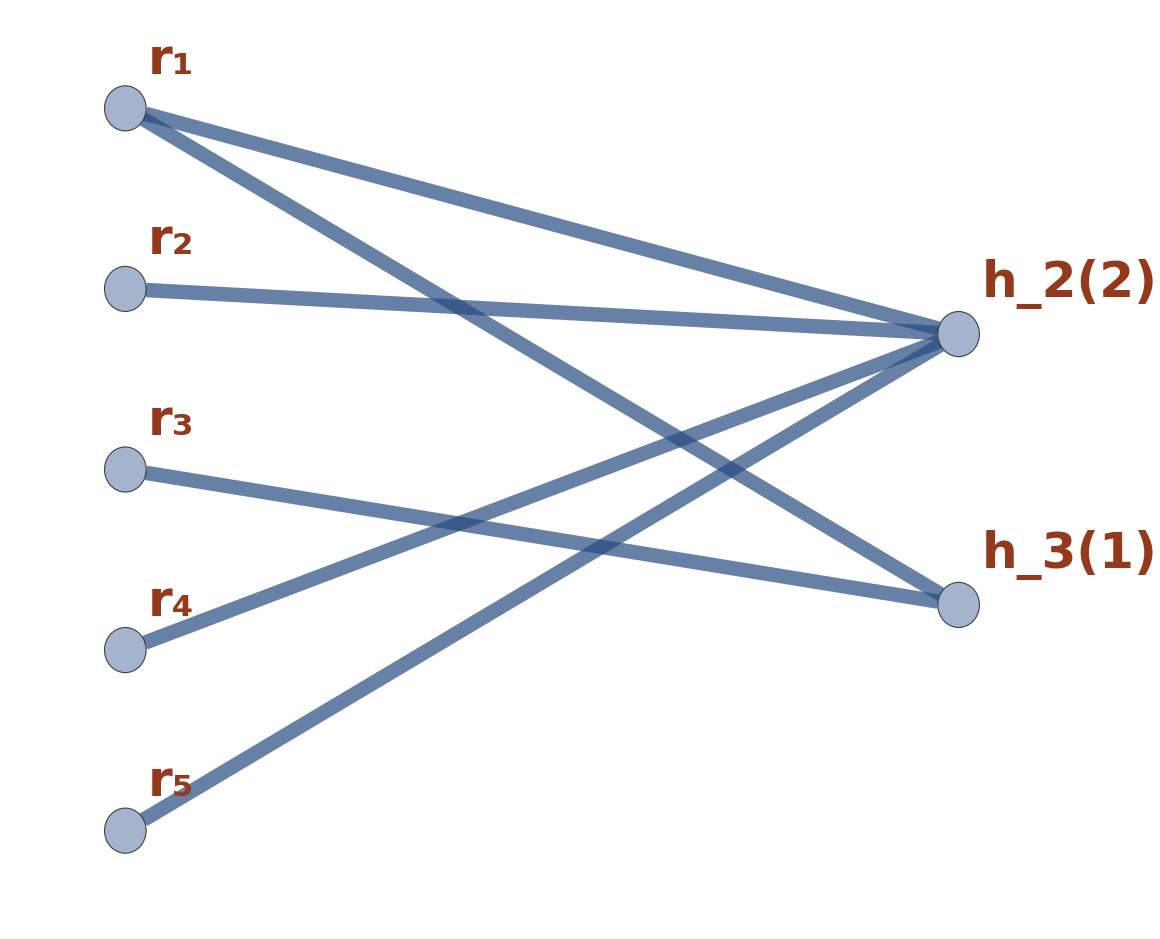

```mathematica
11
```

## Формирование редуцированного графа временных распределений

repeat {
  	while some resident r  is free and has a non-empty list
    		for each hospital h at the head of r’s list {
    			provisionally assign r to h ;
    				if h is fully-subscribed or over-subscribed {
    					for each resident r' dominated on h’s list
    						delete the pair (r', h) } }
    	form the reduced provisionary assignment graph ;
    	find the critical set Z of residents ;
    	for each hospital h  N(Z)
    		for each resident r  in the tail of h’s list
    			delete the pair (r , h) ;
   } until Z == ∅;
   let G be the final provisional assignment graph ;
   let M be a feasible matching in G ;
   if M is strongly stable 
   	output M ;
   else
   	no strongly stable matchings exists;

```mathematica
12
```

## Связанная пара в графе временных распределений

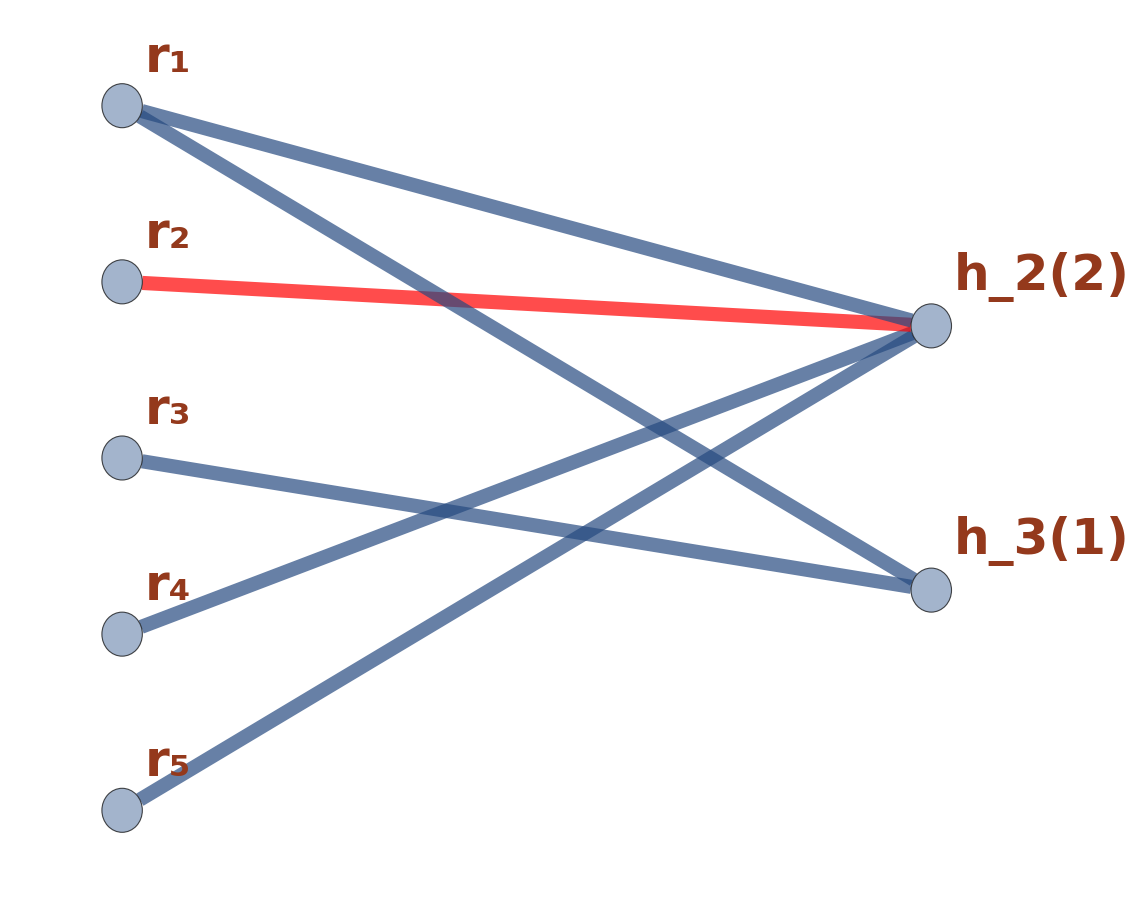

```mathematica
13
```

## Редуцированный граф временных распределений

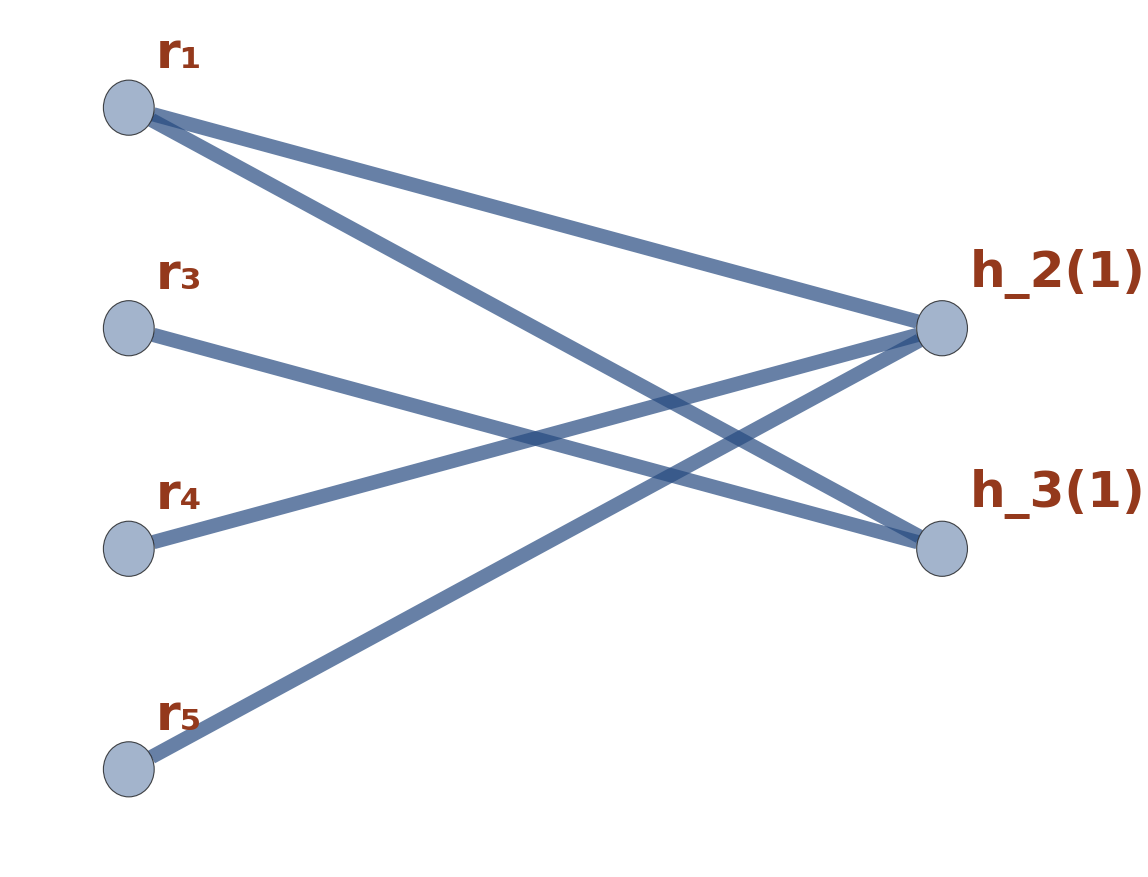

```mathematica
14
```

## Формирование критического множества

repeat {
  	while some resident r  is free and has a non-empty list
    			for each hospital h at the head of r’s list {
    			provisionally assign r to h ;
    				if h is felly-subscribed or over-subscribed {
    					for each resident r' dominated on h’s list
    						delete the pair (r', h) } }
    	form the reducedprovisionaryl assignment graph ;
    	find the critical set Z of residents ;
    	for each hospital h  N(Z)
    		for each resident r  in the tail of h’s list
    			delete the pair (r , h) ;
   } until Z == ∅;
   let G be the final provisional assignment graph ;
   let M be a feasible matching in G ;
   if M is strongly stable 
   	output M ;
   else
   	no strongly stable matchings exists;

```mathematica
15
```

## Формирование критического множества

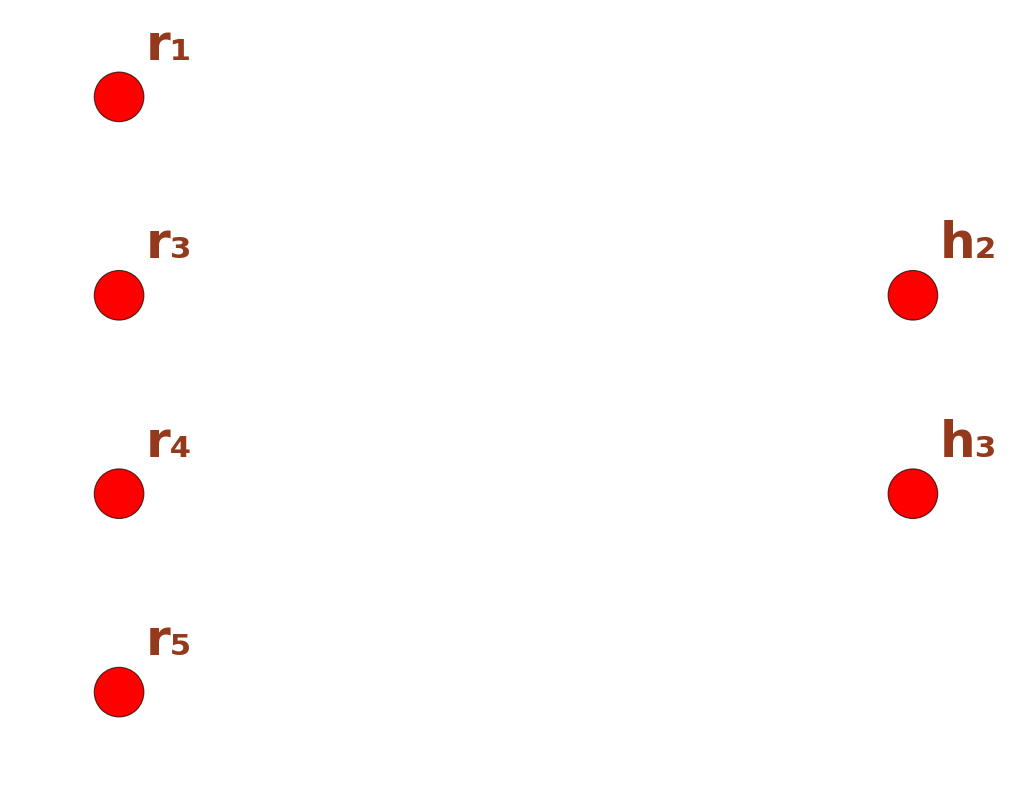

```mathematica
16
```

## Критическое множество в списках предпочтений

Список предпочтений резидентов | Список предпочтений госпиталей
 | 
r_1 | {{h_2,h_3},{h_1}}
r_2 | {h_2,{h_1}}
r_3 | {{h_3},{h_2},{h_1}}
r_4 | {{h_2},{h_3}}
r_5 | {{h_2},{h_1,h_3}} | h_1 | {{r_2},{r_1,r_3},{r_5}} | 3
h_2 | {{r_3},{r_2},{r_1,r_4,r_5}} | 2
h_3 | {{r_4,r_5},{r_1,r_2}} | 1

```mathematica
17
```

## Удаление критического множества

Список предпочтений резидентов | Список предпочтений госпиталей
 | 
r_1 | {{h_2,h_3},{h_1}}
r_2 | {h_2,{h_1}}
r_3 | {{h_3},{h_2},{h_1}}
r_4 | {{h_2},{h_3}}
r_5 | {{h_2},{h_1,h_3}} | h_1 | {{r_2},{r_1,r_3},{r_5}} | 3
h_2 | {{r_3},{r_2},{r_1,r_4,r_5}} | 2
h_3 | {{r_4,r_5},{r_1,r_2}} | 1

```mathematica
18
```

## Вторая итерация: формирование графа временных распределений

Список предпочтений резидентов | Список предпочтений госпиталей
 | 
r_1 | {{h_2,h_3},{h_1}}
r_2 | {h_2,{h_1}}
r_3 | {{h_3},{h_2},{h_1}}
r_4 | {{h_2},{h_3}}
r_5 | {{h_2},{h_1,h_3}} | h_1 | {{r_2},{r_1,r_3},{r_5}} | 3
h_2 | {{r_3},{r_2},{r_1,r_4,r_5}} | 2
h_3 | {{r_4,r_5},{r_1,r_2}} | 1

```mathematica
19
```

## Граф временных распределений со связанными парами

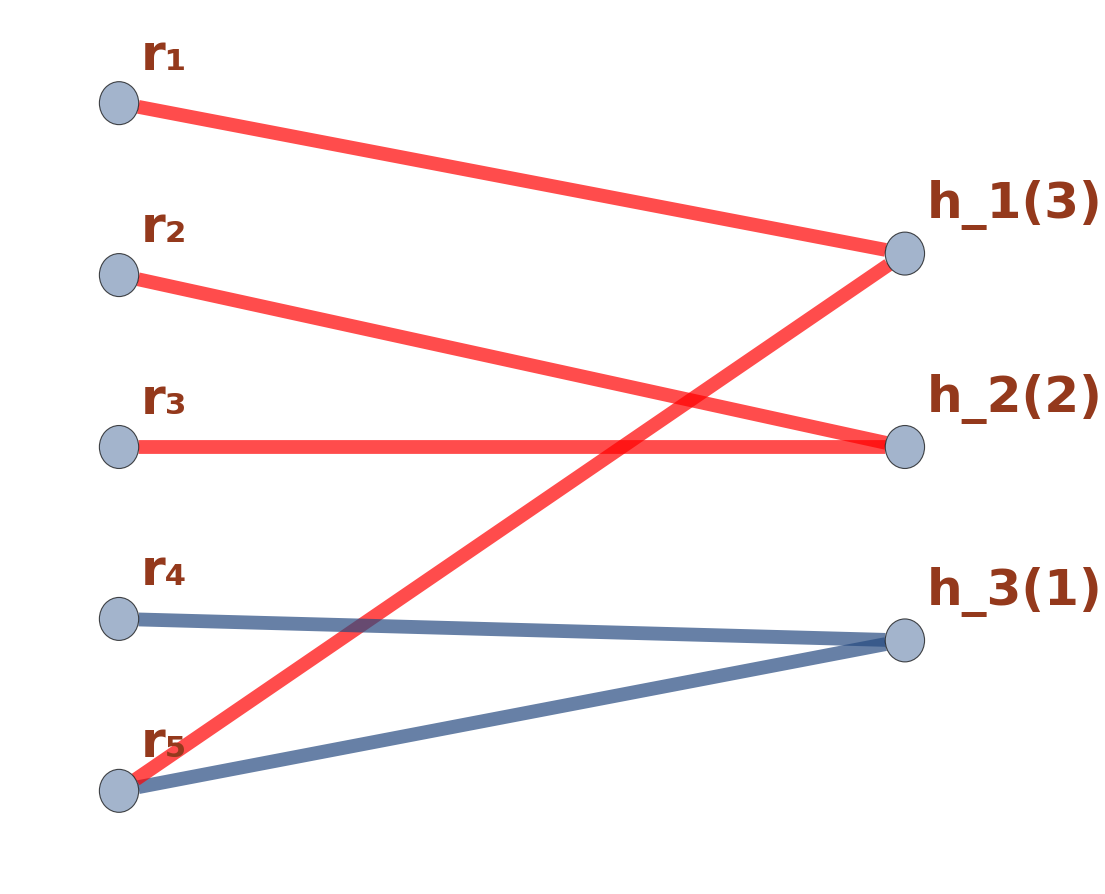

```mathematica
20
```

## Редуцированный граф временных распределений и формирование критического множество

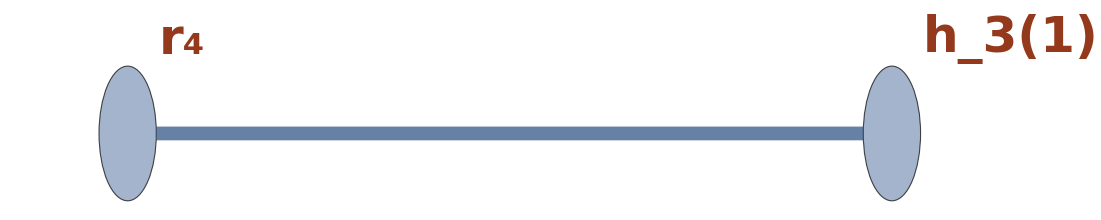

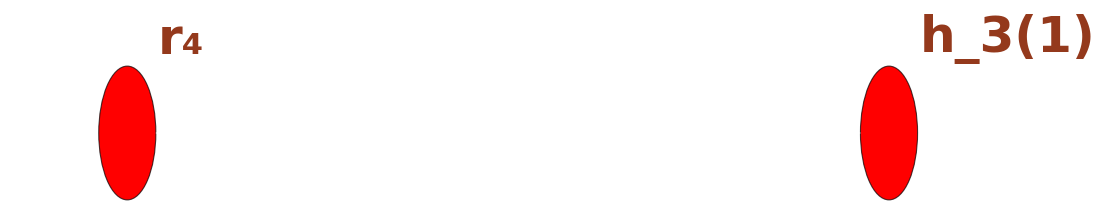

```mathematica
21
```

## Критическое множество в списках предпочтений

Список предпочтений резидентов | Список предпочтений госпиталей
 | 
r_1 | {{h_2,h_3},{h_1}}
r_2 | {h_2,{h_1}}
r_3 | {{h_3},{h_2},{h_1}}
r_4 | {{h_2},{h_3}}
r_5 | {{h_2},{h_1,h_3}} | h_1 | {{r_2},{r_1,r_3},{r_5}} | 3
h_2 | {{r_3},{r_2},{r_1,r_4,r_5}} | 2
h_3 | {{r_4,r_5},{r_1,r_2}} | 1

удаления критического множества не происходит

```mathematica
22
```

## Сильно стабильное распределение

связанные пары (r_1, h_1),(r_2, h_2),(r_3, h_2),(r_5, h_1)

ребра, оставшиеся в редуцированном графе временных распределений (r_4, h_3)

сильнно стабильное распределение:(r_1, h_1),(r_2, h_2),(r_3, h_2),(r_4, h_3),(r_5, h_1)

Список предпочтений резидентов | Список предпочтений госпиталей
 | 
r_1 | {{h_2,h_3},{h_1}}
r_2 | {{h_2},{h_1}}
r_3 | {{h_3},{h_2},{h_1}}
r_4 | {{h_2},{h_3}}
r_5 | {{h_2},{h_1,h_3}}
r_6 | {h_3} | h_1 | {{r_2},{r_1,r_3},{r_5}} | 3
h_2 | {{r_3},{r_2},{r_1,r_4,r_5}} | 2
h_3 | {{r_4,r_5},{r_1,r_2},{r_6}} | 1

```mathematica
23
```

## Тестирование

```mathematica
{listOfResPref,listOfHospPref}=getInitialData["test3"];
show[listOfResPref,listOfHospPref]
```

```mathematica
matching = matchingHRT[listOfResPref,listOfHospPref]
strongStableMatchQ[matching]
```

```mathematica
visualization[matching]
```

```mathematica
24
```

## Спасибо за внимание

```mathematica
Clear@repleteQ 
repleteQ[graph_, h_, q_]:= Length[Cases[graph,{r_,h}:> r]]>=q

Clear@deleteDominated 
deleteDominated[graph_,h_,q_,prefOfHosp_,associationRes_]:= Module[
	{res =Cases[graph,{r_,h}:> r],
	newPrefOfHosp = prefOfHosp,
	newAssociationRes = associationRes,
	newGraph = graph,
	delete, dominated},
	delete =Max[Sort[Position[prefOfHosp,#]⟦1,1⟧&/@res]⟦;;q⟧];
	dominated=Flatten[ newPrefOfHosp⟦delete+1;;⟧];
	newGraph = DeleteCases[newGraph,{r_,h}/;MemberQ[dominated,r]];
	newPrefOfHosp = newPrefOfHosp⟦;;delete⟧;
	(newAssociationRes[#] = DeleteCases[newAssociationRes[#],h,2])&/@dominated;
	(newAssociationRes[#] = DeleteCases[newAssociationRes[#],{}])&/@dominated;
	{newGraph,newPrefOfHosp,newAssociationRes}]

Clear@deleteEmptyRes
deleteEmptyRes[setOfRes_,assRes_]:= Module[{set = setOfRes},
	(If[assRes[#] == {}, set = DeleteCases[set,#]])&/@setOfRes; set]

Clear@deleteBound
deleteBound[graph_,assRes_,assHosp_, ph_]:= Module[
	{rgraph = graph, n = Length@graph,bound = {}, r, h, mph = ph},
	Table[
		r = graph⟦i,1⟧;
		h = graph⟦i,2⟧;
		If[Position[assHosp[h],r]⟦1,1⟧≠ Length@assHosp[h] || mph[h]≥ Length[ Cases[graph,{_,h}]],
			rgraph = DeleteCases[rgraph,{r,h}];mph[h] = mph[h]-1;AppendTo[bound,{r,h}];rgraph= DeleteCases[rgraph,{r,_}]],
	{i,n}];
	{rgraph,bound,ph}]

Clear@findCriticalSet 
findCriticalSet[rgraph_,assRes_,assHosp_,ph_]:= Module[
	{res= assRes,hosp = assHosp, g = rgraph,  nZ = DeleteDuplicates[Last@#&/@rgraph],
	Z = DeleteDuplicates[First@#&/@rgraph],  n ,m, h,r, tail, residents },
	n  = Length@nZ;
	Table[h = nZ⟦i⟧;
		tail = Last@hosp[h];
		residents =Cases[ g,{x_,h}:> x];
		m = Length@residents;
		Table[
			r = residents⟦j⟧;
			If[MemberQ[tail,r] && Position[hosp[h],r]⟦1,1⟧> ph[h],
			Z = DeleteCases[Z,r];
			res[r] = DeleteCases[res[r],h,{2}];
			hosp[h]= DeleteCases[hosp[h],r,{2}]];
			res[r]= DeleteCases[res[r],{}];
			hosp[h]= DeleteCases[hosp[h],{}],
		{j,1,m}],
		{i,1,n}];
	If[Z≠ {},Z = Cases[g,{x_,_}/; MemberQ[Z,x]]];
	{res,hosp,Z}]


Clear@clearEmptyRes
clearEmptyRes[associationRes_]:= DeleteCases[associationRes,{}]

Clear@clearEmptyHosp  
clearEmptyHosp[associationHosp_]:= DeleteCases[associationHosp,{}]

Clear@strongStableMatchQ
strongStableMatchQ[matchings_]:= Module[
	{m = matchings, f = Style["No strongly stable matching exists",45,Hue[0.02,0.88,0.57]]},
	If[ DuplicateFreeQ[m⟦All,1⟧],f = Style["Strongly stable matching",45,Hue[0.33,0.85,0.41]]];
	f]

Clear@matchingHRT 
matchingHRT[listOfResPref_,listOfHospPref_]:=Module[
	{associationRes = <|#⟦1⟧-> #⟦2⟧&/@listOfResPref|>,
	associationHosp = <|#⟦1⟧-> #⟦2⟧&/@listOfHospPref|>,
	quotaList = <|#⟦1⟧-> #⟦3⟧&/@listOfHospPref|>,
	criticalSet={},
	setOfRes, headOfPref, resInGraph, graph, reducedGraph, bound, r, h},
	While[criticalSet == {},
		graph ={};
		setOfRes= Keys[associationRes];
		While[ setOfRes ≠ {},
			r = setOfRes⟦1⟧;
			headOfPref = associationRes[r]⟦1⟧;
			Table[
				h = j;
				AppendTo[graph, {r,h}];
				If[
					repleteQ[graph, h, quotaList[h]],
					{graph ,associationHosp[h] ,associationRes} = deleteDominated[graph,h,quotaList[h],associationHosp[h],associationRes]],
			{j,headOfPref}];
			resInGraph = First/@graph;
			setOfRes = deleteEmptyRes[Complement[setOfRes,resInGraph],associationRes] 
			];
		{reducedGraph ,bound,quotaList}=deleteBound[graph,associationRes,associationHosp,quotaList];
		{associationRes,associationHosp,criticalSet}=findCriticalSet[reducedGraph,associationRes,associationHosp,quotaList];
    associationRes=clearEmptyRes[associationRes];
    associationHosp=clearEmptyHosp[associationHosp];
	]; 
	Join[bound,criticalSet]]
```

```mathematica
Clear@show
show[listOfResPref_,listOfHospPref_]:=Grid[{{Style[listOfResPref//MatrixForm,45],Style[listOfHospPref//MatrixForm,45]},{}}]
```

```mathematica
Clear@visualization
visualization[x_]:=Which[ 
x == {{Subscript["r", 2],Subscript["h", 5]},{Subscript["r", 5],Subscript["h", 4]},{Subscript["r", 1],Subscript["h", 1]},{Subscript["r", 4],Subscript["h", 5]}},
Graph[{Subscript["r", 5],Subscript["r", 4],Subscript["r", 2],Subscript["r", 1],"h_5(2)","h_4(3)","h_1(1)"},{Style[Subscript["r", 1]<->"h_1(1)",Green],Style[Subscript["r", 2]<->"h_5(2)",Green],Style[Subscript["r", 4]<->"h_5(2)",Green],Style[Subscript["r", 5]<->"h_4(3)",Green],Style[Subscript["r", 1]<->"h_5(2)",Transparent],Style[Subscript["r", 5]<->"h_5(2)",Transparent]},ImageSize->850,
VertexLabels->"Name",GraphLayout->"BipartiteEmbedding",EdgeStyle->Thickness[0.009],
VertexSize->0.25,VertexLabelStyle->Directive[Hue[0.04,0.81,0.58],35]],
x== {{Subscript["r", 1],Subscript["h", 1]},{Subscript["r", 2],Subscript["h", 2]},{Subscript["r", 3],Subscript["h", 2]},{Subscript["r", 5],Subscript["h", 1]},{Subscript["r", 4],Subscript["h", 3]}},
Graph[{Subscript["r", 5],Subscript["r", 4],Subscript["r", 3],Subscript["r", 2],Subscript["r", 1],"h_3(1)","h_2(2)","h_1(3)"},{Style[Subscript["r", 1]<->"h_2(2)",Transparent],
Style[Subscript["r", 1]<->"h_1(3)",Green],Style[Subscript["r", 2]<->"h_2(2)",Green],
Style[Subscript["r", 3]<->"h_2(2)",Green],Style[Subscript["r", 4]<->"h_3(1)",Green],Style[Subscript["r", 5]<->"h_1(3)",Green],Style[Subscript["r", 5]<->"h_3(1)",Transparent]},ImageSize->850,
VertexLabels->"Name",GraphLayout->"BipartiteEmbedding",EdgeStyle -> Thickness[0.009],
VertexSize->0.25,VertexLabelStyle->Directive[Hue[0.04,0.81,0.58],35]],
x == {{Subscript["r", 1],Subscript["h", 2]},{Subscript["r", 2],Subscript["h", 4]},{Subscript["r", 4],Subscript["h", 2]},{Subscript["r", 5],Subscript["h", 2]},{Subscript["r", 6],Subscript["h", 3]},{Subscript["r", 7],Subscript["h", 1]},{Subscript["r", 9],Subscript["h", 2]},{Subscript["r", 10],Subscript["h", 1]},{Subscript["r", 3],Subscript["h", 4]},{Subscript["r", 8],Subscript["h", 4]}},Graph[{Subscript["r", 10],Subscript["r", 9],Subscript["r", 8],Subscript["r", 7],Subscript["r", 6],Subscript["r", 5],Subscript["r", 4],Subscript["r", 3],Subscript["r", 2],Subscript["r", 1],"h_4(3)","h_3(1)","h_2(5)","h_1(2)"},
{Style[Subscript["r", 1]<->"h_2(5)",Green],Style[Subscript["r", 2]<->"h_4(3)",Green],Style[Subscript["r", 4]<->"h_2(5)",Green],Style[Subscript["r", 5]<->"h_2(5)",Green],Style[Subscript["r", 6]<->"h_3(1)",Green],Style[Subscript["r", 7]<->"h_1(2)",Green],Style[Subscript["r", 8]<->"h_4(3)",Green],Style[Subscript["r", 9]<->"h_2(5)",Green],Style[Subscript["r", 10]<->"h_1(2)",Green],Style[Subscript["r", 3]<->"h_4(3)",Green],Style[Subscript["r", 2]<->"h_1(2)",Transparent],Style[Subscript["r", 1]<->"h_1(2)",Transparent],Style[Subscript["r", 6]<->"h_1(2)",Transparent]},ImageSize-> 1050,
VertexLabels->"Name",GraphLayout->"BipartiteEmbedding",EdgeStyle->Thickness[0.007],
VertexSize->0.50,VertexLabelStyle->Directive[Hue[0.04,0.81,0.58],30]],
x=={{Subscript["r", 1],Subscript["h", 3]},{Subscript["r", 2],Subscript["h", 3]},{Subscript["r", 3],Subscript["h", 4]},{Subscript["r", 4],Subscript["h", 2]},{Subscript["r", 5],Subscript["h", 5]},{Subscript["r", 6],Subscript["h", 5]},{Subscript["r", 6],Subscript["h", 2]}},Graph[{Subscript["r", 6],Subscript["r", 5],Subscript["r", 4],Subscript["r", 3],Subscript["r", 2],Subscript["r", 1],"h_5(2)","h_4(1)","h_3(3)","h_2(2)"},
{Style[Subscript["r", 1]<->"h_3(3)",Green],
Style[Subscript["r", 2]<->"h_3(3)",Green],
Style[Subscript["r", 4]<->"h_2(2)",Green],
Style[Subscript["r", 3]<->"h_4(1)",Green],
Style[Subscript["r", 3]<->"h_5(2)",Transparent],
Style[Subscript["r", 5]<->"h_5(2)",Green],
Style[Subscript["r", 6]<->"h_5(2)",Red],
Style[Subscript["r", 6]<->"h_2(2)",Red],
Style[Subscript["r", 1]<->"h_5(2)",Transparent]},ImageSize->850,
VertexLabels->"Name",GraphLayout->"BipartiteEmbedding",EdgeStyle->Thickness[0.009],
VertexSize->0.25,VertexLabelStyle->Directive[Hue[0.04,0.81,0.58],35]]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
getInitialData[name_]:=Get[name]
```

```mathematica
$Line=0;
```

```mathematica
25
```